```mathematica
Quit
```

```mathematica
LGet["Tetration"]
ClearSystemCache[];CC
```

所有临时定义已清空!

```mathematica
NSeries[Exp[x],{x,0,5}]//Chop
```

1.+x+0.5 x^2+0.166667 x^3+0.0416667 x^4+0.00833333 x^5+O[x]^6

```mathematica
NSeries[HalfExp[x],{x,0,5}]
```

LessEqual::nord: 尝试使用 0.980785+0.19509 ⅈ 进行无效的比较.

LessEqual::nord: 尝试使用 0.92388+0.382683 ⅈ 进行无效的比较.

General::stop: 在本次计算中，LessEqual::nord 的进一步输出将被抑制.

NSeries[HalfExp[x],{x,0,5}]

```mathematica
HalfExp[E,1.44461]
```

2.35284

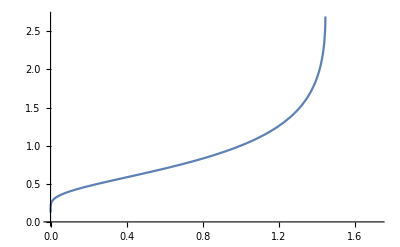

```mathematica
Plot[Tetrate[x,Infinity],{x,0,E-1}]
```

TetraDFormat[…]

TetraDFormat[…]

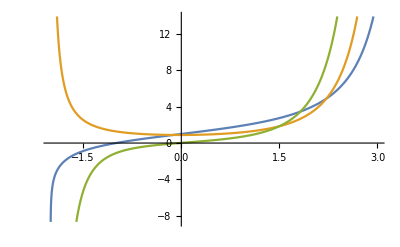

```mathematica
td=TetraD[Tetrate[2,x],x]
td2=TetraD[Tetrate[2,x],{x,2}]
Plot[{Tetrate[2,x],td[x],td2[x]},{x,-2,3}]
```

TetraDFormat[…]

TetraDFormat[…]

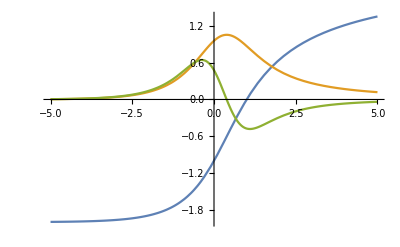

```mathematica
td=TetraD[TetraLog[3,x],x]
td2=TetraD[TetraLog[3,x],{x,2}]
Plot[{TetraLog[3,x],td[x],td2[x]},{x,-5,5}]
```

TetraDFormat[…]

TetraDFormat[…]

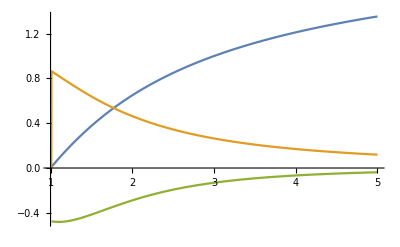

```mathematica
td=TetraD[TetraRoot[3,x],x]
td2=TetraD[TetraRoot[3,x],{x,2}]
Plot[{TetraRoot[3,x],td[x],td2[x]},{x,1,5}]
```

```mathematica
$Line=0
```

0

```mathematica
Quit
```

```mathematica
CC
```

所有临时定义已清空!

```mathematica
Unprotect[FunctionExpand]
```

```mathematica
FullSimplify[D[ProductLog[-Log[z]]/-Log[z],z],z>0]
```

ⅇ^(-2 ProductLog[-Log[z]])/(z+z ProductLog[-Log[z]])

```mathematica
TetraTower[z_?NumericQ]:=ProductLog[-Log[z]]/-Log[z];
Format[TetraTower[z_?AtomQ],TraditionalForm]:=DisplayForm@Tooltip[
RowBox[{SuperscriptBox["","∞"],"",z}],
"TetraTower"]
Format[TetraTower[z_],TraditionalForm]:=DisplayForm@Tooltip[
RowBox[{SuperscriptBox["","∞"],"(",z,")"}],
"TetraTower"]
```

```mathematica
TetraTower/: Derivative[1][TetraTower]:=Function[
{z},
1/(E^(2*ProductLog[-Log[z]])*
   (z + z*ProductLog[-Log[z]]))
]
```

```mathematica
1/(E^(2*ProductLog[-Log[z]])*
   (z + z*ProductLog[-Log[z]]))
```

ⅇ^(-2 ProductLog[-Log[z]])/(z+z ProductLog[-Log[z]])

```mathematica
Solve[ProductLog[-Log[z]]/-Log[z]==x,z]//FullSimplify
```

Solve::ifun: Solve 正在使用反函数，因此可能无法找到某些解；请使用 Reduce 来获取完整的解信息.

{{z→(1/x)^(-1/x)}}

```mathematica
FullSimplify[Log[z]TetraTower[z],z>0]
```

Log[z] TetraTower[z]

```mathematica
TetraSSR[z_?NumericQ]:=(1/z)^(-1/z);
Unprotect[InverseFunction,FunctionExpand]
FunctionExpand@TetraTower[z_]:=ProductLog[-Log[z]]/-Log[z];
FunctionExpand@TetraSSR[z_]:=z^(1/z);
InverseFunction[TetraTower]=TetraSSR;
InverseFunction[TetraSSR]=TetraTower;
```

{}

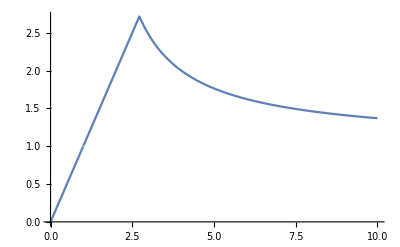

```mathematica
Plot[TetraTower[TetraSSR[x]],{x,0,10}]
```

```mathematica
HyperFactorial
```